# THE MULTISCALE NATURE OF DEFORMATION AND METAMORPHISM

Alison Ord

Flip Phillips

## Background

Hobbs & Ord (2015) is concerned with the processes that operate during the deformation and metamorphism of rocks in the crust and upper lithosphere of the Earth. The deformation and metamorphism of rocks involves structural rearrangements of elements of the rock at the microscale by processes such as mass diffusion, dislocation slip and climb, grain-boundary migration and fracturing at the same time as chemical reactions proceed. In some instances infiltrating fluids introduce or remove chemical components and may influence mechanical properties through changes in mineralogical composition, fluid pressure or temperature. At the same time, heat is added to or removed from the system depending on the surrounding tectonic environment. Such mechanisms do not operate independently of each other but are coupled so that each process has feedback influences on the others leading to structures and mineral assemblages that do not develop in the uncoupled environment.

Its contents are represented by this Word Cloud.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School"]
image=Import["hobbs&ord2015WordCloud.jpg"];
imageshow=ImageResize[image,Large]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School

-Graphics-

This computational essay is a first step towards developing the application of the tools of nonlinear dynamics to measuring rocks, to measuring the structural architectures which result from processes interacting and developing in a coupled environment.

## Vision

The vision for mathematica is of moving a cursor through (x, y, z) coordinates for the surface of a deformed, folded rock and to watch data driven analyses change in different windows including : spatial attractors, wavelet transforms, singularity spectra, Hurst exponents, recurrence plots (including the ability for cross - and joint - recurrence plots and their quantitative analysis), Fourier transforms, recurrence histograms, networks, and sparsely determined nonlinear determinations of the differential equations describing the data.

## Step 1

Are folded rocks a snapshot of a nonlinear dynamic system? When layered rocks are shortened during tectonic events, the most obvious structures formed are folds. Folding of layered rocks causes a change in geological structure that can lead to a fundamental modification of the mechanical and hydraulic properties of the rock mass across several orders of magnitude in length - typically from the millimetre to the kilometre-scale. 

The understanding of how, why and on which scale folding occurs therefore has fundamental implications for problems in geology and engineering, including prediction of the form and location of hydrocarbon accumulations, salt domes, groundwater flow, mineralization, and rock slope stability.

We have prepared three dimensional models of natural fold systems using photogrammetry and we explore the multifractal geometry using wavelet transforms and recurrence quantification in order to delineate the dynamics of naturally folded systems.

## The Data

### Surfaces of folded rocks

First we see a multiply deformed rock with porphyroblasts from Rum Jungle in Australia.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\RumJungle images"]
"C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\RumJungle images"
image=Import["20171001-199A8116.jpg"];
imageshow=ImageResize[image,Medium]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\RumJungle images

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\RumJungle images

-Graphics-

It is then photographed from multiple angles, and the images collated and analysed within CloudCompare. This image shows interpreted cloud of points, with a single line through the points denoting the data collected, and shown in cross section in the following figure.

```mathematica
image=Import["Ord_C_profile_3.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

Here is another multiply folded rock, this time from Broken Hill in Australia. First, we look at the rock, sitting on a structured page used for collating the photographic images.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
"C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"
image=Import["20171001-199A8030.jpg"];
imageshow=ImageResize[image,Medium]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

-Graphics-

Second, we see the cloud of points for that system, derived from the photo collection.

```mathematica
image=Import["Ord_samp_1.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

Third, we have the cloud of points just of the rock, followed by a section through the rock cloud,

```mathematica
image=Import["sections.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

```mathematica
image=Import["sections4.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

and an imported version of the cross section.

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

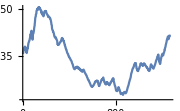

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
"C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"
data=ReadList["rock4z"];
datalist=Flatten[data];
ListPlot[datalist,PlotRange->All,Joined->True,ImageSize->Small]
```

## The Analyses

### Spatial attractors

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"]
"C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx8192m"];
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

Here we show the spatial attractor for the data with a lag of 20, in various styles.

```mathematica
m=Import["Section contour #4 lag 1.xlsx",{"Sheets",3}];
```

```mathematica
ListPointPlot3D[m,DataRange->Automatic,ColorFunctionScaling->True,ColorFunction->"Rainbow",Axes->True,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{t,t+20,t+40},ImageSize->Small]
```

-Graphics3D-

```mathematica
junk=BSplineCurve[{m}];
Tube[junk];
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20,i+40},ViewPoint->{-2,2,0},ImagePadding->4,ImageSize->Small]
```

-Graphics3D-

### Wavelet transforms

ContinuousWaveletData[…]

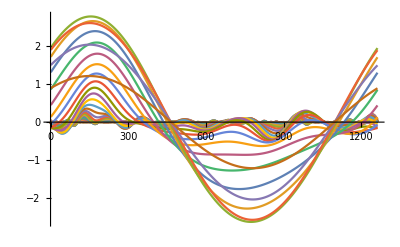

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
cwd[All,"Values"];
recwd=Re[%];
cwd[{"WaveletScale","Octaves","Voices"}];
ListLinePlot[recwd,PlotRange->All]
```

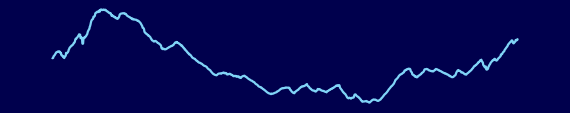
-Graphics-
-Graphics-

```mathematica
cf[x_]:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,0.5],RGBColor[0,0.1,0.5],RGBColor[0,0.2,1],RGBColor[0,0.5,1],RGBColor[0.2,0.7,1],RGBColor[0.5,0.8,1],RGBColor[0.5,.9,.9],RGBColor[0.5,1.,0.9],RGBColor[0.7,1,0.7],RGBColor[0.8,1,0.5],RGBColor[1,1,0],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,.25,0],RGBColor[1,.1,0.],RGBColor[1,.0,0.],RGBColor[.9,.0,0.],RGBColor[0.8,0.,0.],RGBColor[0.5,0.,0.],RGBColor[.25,0.,0.],RGBColor[0.1,0,0]},x];
Column[{ListLinePlot[datalist,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[recwd,ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

### Singularity spectra

The singularity spectra are presently created using Last Wave. See Bacry et al. (1993) and Arneodo et al. (2008).

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"];
imageshow=ImageResize[Import["rock4zSingSpec.jpg"],Medium]
```

-Graphics-

### Recurrence plots

Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
(* <<RQA` *)
```

The package is built on the equations expressed in Webber and Marwan (2015).

## Load the data

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

```mathematica
(* data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","r30datab.dat"}]]] ; *)
```

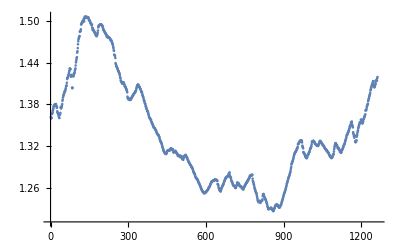

```mathematica
ListPlot[data]
```

We create a time series in the form required by mtca.

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

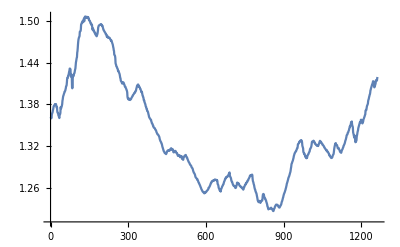

```mathematica
ListLinePlot[ds]
```

## Estimate the lag and embedding dimensions for the data

The lag is first estimated-

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

However, a lag of 10 was used in previously published work (Ord&Hobbs, 2018; Ord et al., 2018) so that is what we will use here.

```mathematica
lag=10
```

10

The embedding dimension of the system is then estimated. The result below suggests a dimension of 3.

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.40655,1262,4.72984×10^-8,1252,1.41325×10^-6},{3,0.0990338,1252,1.41325×10^-6,1242,2.94388×10^-6},{4,0.023539,1242,2.94388×10^-6,1232,4.36527×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

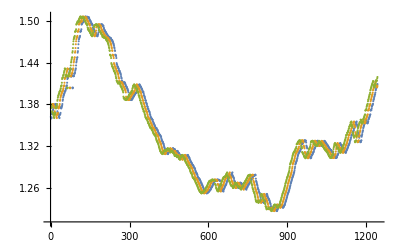

```mathematica
ListPlot[embedding]
```

## Plot the 3D spatial attractor

embedding is now a list of 3 columns of data, off set by the lag of 10, and we plot these in three dimensions, with the axes representing t, t+10, t+20

```mathematica
ParametricPlot3D[embedding[t],{t,1,650},ImageSize->Small]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]},ViewPoint->{Left,Top},ImageSize->Small]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]],ViewPoint->{Left,Bottom},ImageSize->Small]
```

-Graphics3D-

## Calculate the distance map and the recurrence map

Numerical examples provide explicit step-by-step details on how input vectors (data) are delayed, embedded, normed, and rescaled to define elements (distances) in the distance matrix (DM). Also described is how the recurrence matrix (RM) is derived from the DM by selecting only those recurrent points with distances falling within a selected RADIUS. Understanding of these simple examples should remove the mathematical mystery behind the basis of recurrence quantification analysis which simply finds patterns among recurrent points according to objective rules. Webber (2012)

Webber Chap 2.pdf the radius parameter implements a cut-off limit that transforms the distance matrix (DM) into the recurrence matrix (RM). That is, all (i, j) elements in DM with distances at or below the RADIUS cutoff are included in the recurrence matrix (element value = 1), but all other elements are excluded from RM (element value = 0). The RM derives from the DM, but the two matrices are not identical.

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the distance map

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

The minimum and maximum are  determined to be 0 and 0.224875

```mathematica
MinMax[dm]
```

{0.,0.224875}

with dimensions

```mathematica
Dimensions[dm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[dm]]
```

1242

From the RQA package, the automatic radius for rock4z is 0.0340171

```mathematica
Mean[Flatten[dm]]
```

0.0340171

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map

```mathematica
rm=RQARecurrenceMap[embedding];
```

The recurrence map may be plotted

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

## Calculate the RQA measures; compare with those using Webber’s RQA software

```mathematica
N[RQARecurrence[rm]]
```

0.680771

This compares with %REC=40.2 which is the result from Webber’s RQA for embedding dimension of 3 and a lag of 10

```mathematica
N[RQADeterminism[rm]]
```

0.999567

%DET=99.9 Result from RQA

```mathematica
N[RQALaminarity[rm,3]]
```

0.999178

%LAM=100 Result from RQA

```mathematica
N[RQATrappingTime[rm]]
```

220.737

TT=121.8 Result from RQA

```mathematica
N[RQATrend[rm]]
```

General::munfl: Exp[-3203.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1413.91] is too small to represent as a normalized machine number; precision may be lost.

-30.6973

Trend -56.4 Result from RQA

```mathematica
N[RQAEntropy[rm]]
```

8.02657

Entropy 7.6 Result from RQA

```mathematica
N[RQAChaos[rm]]
```

0.000805802

Result from RQA ? 1/DMAX

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the maximum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots. You can change DMAX by changing the first part of the Range. For example, for @Range[500,w-1] DMAX=319, and for @Range[1000,w-1] DMAX=134

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

why has this stopped working? changed threshold to 3 - it worked. changed threshold to 2 - it worked. ? !

```mathematica
RQADmax[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«45»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1143»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

segmentLengths[{1},2.]
 |  |  |  |

DMAX 1241 Result from RQA

1/DMax = ‘chaos’ as expected. ‘chaos’ is the maximum Lyapunov exponent. Note that the 2 here is the magnitude of the line required to be stated in the Webber code.

```mathematica
1/%
```

1/segmentLengths[{1},2.]
 |  |  |  |

=1/chaos - as expected

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,2]
```

segmentLengths[{1},2]
 |  |  |  |

VMAX -592 Result from RQA

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
RQADetnew[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«45»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1143»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

Total::tllen: Lists of unequal length in {{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1191»},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1190»},«48»,«1191»} cannot be added.

1.90605×10^-6 Total[segmentLengths[Total[{1}],2.]]
 |  |  |  |

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
RQARecurnew[rm]//N
```

0.680771

Marwan&Webber Equation 1.11

```mathematica
RQARatio=N[RQARecurrence[rm]]/N[RQADeterminism[rm]]
```

0.681066

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
Manipulate[ListLinePlot[Take[data,{x,x+200}]],{{x,1},1,1200},SaveDefinitions->True,FrameLabel->"saved"]
```

```mathematica
ds["Properties"];
```

```mathematica
dsw=TimeSeriesWindow[ds,{1,1242}]
```

TimeSeries[…]

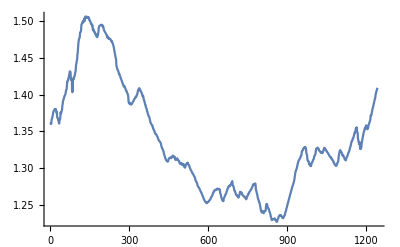

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

```mathematica
embedLag=RQAEstimateLag[ds]
```

305.726

```mathematica
RQAEstimateDimensionality[ds,embedLag]
```

4.72984×10^-7

{Null,{{{2,0.35251,1262,4.72984×10^-8,956,1.38088×10^-6},{3,0.0661538,956,1.38088×10^-6,650,2.69822×10^-6},{4,0.0116279,650,2.69822×10^-6,344,4.23066×10^-6}}}}

## Time Series Epochs start here

```mathematica
eps=RQATimeSeriesEpochs[dsw,400,200];
```

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{89.5272,139.201,146.776,146.776,146.776}

```mathematica
Mean[%]
```

133.811

RQAEmbed::usage=”RQAEmbed[ts,dims,tau].”

```mathematica
embeds=Map[RQAEmbed[#,3,10.0]&,eps];
```

```mathematica
maps=RQADistanceMap/@embeds;
```

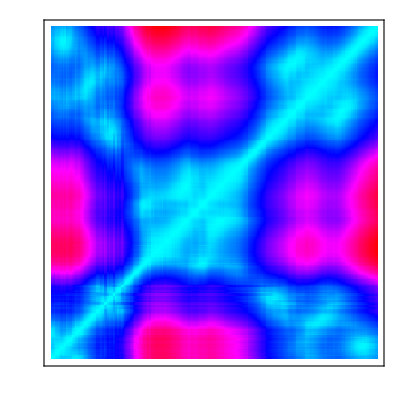
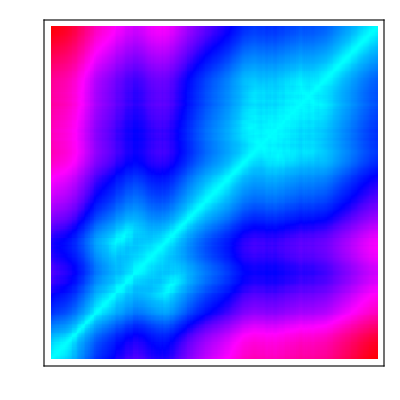
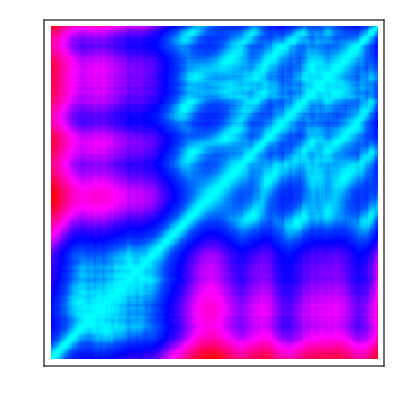
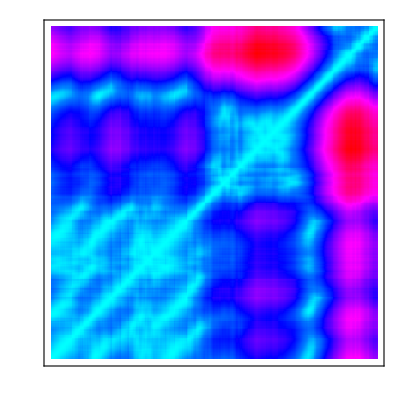
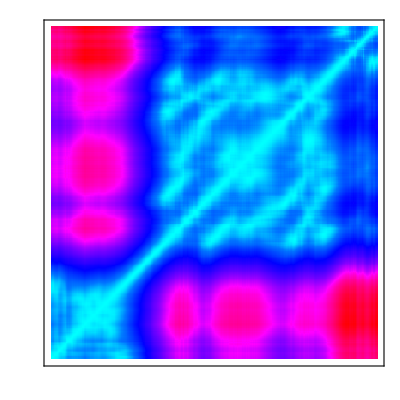

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@maps
```

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

and for the recurrence map

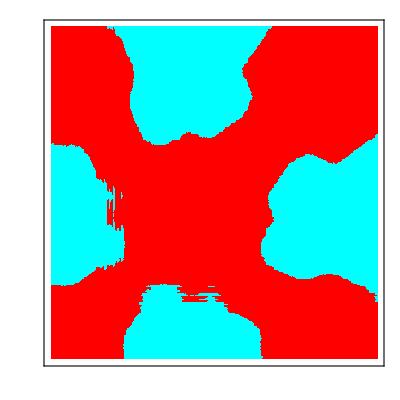
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@numbers
```

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)];
```

The numbers are different for the epoch rm’s than for the main rm so the patterns do not map so obviously to each other.

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
TabView[{"Rec"->ListLinePlot[N[RQARecurrence/@numbers]],"Det"->ListLinePlot[N[RQADeterminism/@numbers]],"Lam"->ListLinePlot[N[RQALaminarity/@numbers]],"Trap"->ListLinePlot[N[RQATrappingTime/@numbers]],"Trend"->ListLinePlot[N[RQATrend/@numbers]],"Entropy"->ListLinePlot[N[RQAEntropy/@numbers]],"Dmax"->ListLinePlot[N[RQADmax/@numbers]],"Vmax"->ListLinePlot[N[RQAVmax/@numbers]],"Chaos"->ListLinePlot[N[RQAChaos/@numbers]]}]
```

General::munfl: Exp[-1023.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1181.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

123456789

#### References

Arneodo A, Audit B, Kestener P, Roux S. 2008 Wavelet-based multifractal analysis. Scholarpedia 3, 4103. (doi:10.4249/scholarpedia.4103)
Bacry E, Muzy JF, Arneodo A. 1993 Singularity spectrum of fractal signals from wavelet
analysis: exact results. J. Stat. Phys. 70, 635–674. (doi:10.1007/BF01053588)
Hobbs BE, Ord A. 2015 Structural geology: the mechanics of deforming metamorphic rocks.
Amsterdam, The Netherlands: Elsevier.
Hobbs, B.E., Ord, A. Nonlinear dynamical analysis of GNSS data: Quantification, precursors and synchronisation. Progress in Earth and Planetary Science. 2018. https://doi.org/10.1186/s40645-018-0193-6
Kononov E. 2006 VRA Visual Recurrence Analysis. Version 4.9. See http://web.archive.org/web/20070131023353 and http://www.myjavaserver.com/~nonlinear/vra/download.html.
Oberst, S., Niven, R.K., Lester, D.R., Ord, A., Hobbs, B. and Hoffmann, N. Detection of unstable periodic orbits in mineralising geological systems. Chaos 28, 085711 (2018); doi: 10.1063/1.5024134
Ord A. 1994 The fractal geometry of patterned structures in numerical models for rock
deformation. In Fractals and dynamic systems in geoscience (ed. JH Krühl), pp. 131–155. Berlin,
Germany: Springer.
Ord, A. and Hobbs, B.E. Quantitative measures of deformed rocks: the links to dynamics. Journal of Structural Geology, 2018. https://doi.org/10.1016/j.jsg.2018.05.027
Ord, A., Hobbs, B.E., Dering, G. and Gessner, K. Nonlinear analysis of natural folds using wavelet transforms and recurrence plots. Philosophical Transactions of the Royal Society A. 2018. http://dx.doi.org/10.1098/rsta.2017.0257	
Webber Jr CL. 2012 README_2012.PDF (Introduction to Recurrence Quantification Analysis, v 14.1). See http://homepages.luc.edu/~cwebber.